# Traveling Sale Person Project Revised 2

## Quang Vu

## Generate Prerequisite For Exploring The Traveling Sale Person Problem

This is where we generate code for plotting our tour using a list of points and the indexing of the tour.

```mathematica
plotTour[points_,tour_]:=Module[
{n=Length[points],tourPts},
tourPts=Table[0,n+1]; (*initialize list of size n+1*)

(* fill in the cities in order in tourPts *)
Do[
tourPts[[i]]=points[[tour[[i]]]],
{i,1,n}];
tourPts[[n+1]]=points[[tour[[1]]]] ;(* return to starting point *)

(* return the plot *)
ListPlot[tourPts,Joined->True]
]
```

The next code chunk will be out code to calculate the distance of a tour

```mathematica
distTour[points_,tour_]:=Module[
{dist=0},

(* loop over all edges along the tour *)
Do[
dist+=EuclideanDistance[points[[tour[[i]]]],points[[tour[[i+1]]]]],
{i,1,Length[tour]-1}];
dist+=EuclideanDistance[points[[tour[[-1]]]],points[[tour[[1]]]]]; (* return to starting point*)

(* return the distance *)
dist
]
```

## Simulated Annealing For Travelling Sale Person

Let’s use simulated annealing to find (approximately) minimum tours for larger values of n.

### Objective Function

We want to minimize the length of the tour. We already implemented our distTour function that computes this length.

### Transition Function

Unfortunately, we can get into situations where any individual swap will lengthen the tour, but some  combination of simultaneous swaps will shorten the tour. In this case, it can be helpful to reverse a randomly-selected subsequence

```mathematica
proposeMoveReverse[currTour_]:=Module[{n=Length[currTour],i,j,propTour=currTour},
{i,j} = RandomSample[Range[n],2];
If [ i <j,
propTour[[i;;j]]=Reverse[currTour[[i;;j]]];];
propTour]
```

#### Simulated Annealing

```mathematica
findMinTour[points_,βstart_,βinc_,numIter_]:=Module[
{n=Length[points],currTour,currDist,β=βstart,propTour,Δf,fVals=Table[0,numIter],ρ,j,k,jprev,knext,account},
currTour=Range[n];
currDist=distTour[points,currTour];
fVals[[1]]=currDist;
account=0;
Do[propTour=currTour;
{j,k}=RandomSample[Range[n],2];
If[j>k,{j,k}={k,j}];
While[j==1&&k==n,
{j,k}=RandomSample[Range[n],2]];
If[j>k,{j,k}={k,j}];
propTour[[j;;k]]=Reverse[currTour[[j;;k]]];
jprev=If[j>1,j-1,n];
knext=If[k<n,k+1,1];
a=EuclideanDistance[points[[currTour[[k]]]],points[[currTour[[jprev]]]]];
b=EuclideanDistance[points[[currTour[[j]]]],points[[currTour[[knext]]]]];
c=EuclideanDistance[points[[currTour[[j]]]],points[[currTour[[jprev]]]]];
d=EuclideanDistance[points[[currTour[[k]]]],points[[currTour[[knext]]]]];
Δf=a+b-c-d;
β*=βinc;
ρ=Exp[-β*Δf];
If[RandomReal[]<ρ||Δf<0,currTour=propTour;
propTour=Append[propTour,propTour[[1]]];
currDist=currDist+Δf;
account+=1];
fVals[[i]]=currDist;,
{i,2,numIter}];
(*Add the last position to the first position so we have fully connected path jsut like findminTOur in mathematica*)
Print["Shortest tour: ",propTour];
Print["The number of accepting :",account];
Print["Distance of current Tour:", currDist];
{currDist,propTour}]
```

```mathematica
findMinTour[points_,βstart_,βinc_,numIter_]:=Module[{n=Length[points],currTour,currDist,β=βstart,propTour,Δf,fVals=Table[0,numIter],ρ,j,k,jprev,knext,account},currTour=Range[n];
currDist=distTour[points,currTour];
fVals[[1]]=currDist;
account=0;
Do[propTour=currTour;
{j,k}=RandomSample[Range[n],2];
If[j>k,{j,k}={k,j}];
While[j==1&&k==n,{j,k}=RandomSample[Range[n],2]];
If[j>k,{j,k}={k,j}];
propTour[[j;;k]]=Reverse[currTour[[j;;k]]];
jprev=If[j>1,j-1,n];
knext=If[k<n,k+1,1];
a=EuclideanDistance[points[[currTour[[k]]]],points[[currTour[[jprev]]]]];
b=EuclideanDistance[points[[currTour[[j]]]],points[[currTour[[knext]]]]];
c=EuclideanDistance[points[[currTour[[j]]]],points[[currTour[[jprev]]]]];
d=EuclideanDistance[points[[currTour[[k]]]],points[[currTour[[knext]]]]];
Δf=a+b-c-d;
β*=βinc;
ρ=Exp[-β*Δf];
If[RandomReal[]<ρ||Δf<0,currTour=propTour;
currDist=currDist+Δf;
account+=1];
fVals[[i]]=currDist;,{i,2,numIter}];
(*Add the last position to the first position so we have fully connected path*)propTour=Append[propTour,propTour[[1]]];
(*Print["Shortest tour: ",propTour];*)
Print["The number of accepting :",account];
Print["Distance of current Tour:",currDist];
{currDist,propTour}]
```

```mathematica
numPoints=5;
points=RandomReal[1,{numPoints,2}];
{dist, tour} = FindShortestTour[points]
pointPlot=ListPlot[points->Range[numPoints],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[
Graphics[Line[points[[tour]]]],
pointPlot]
```

{2.29924,{1,5,2,4,3,1}}

-Graphics-

```mathematica
{distSA, tourSA} = findMinTour[points,1,1.0001,15500];
pointPlot=ListPlot[points->Range[numPoints],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points[[tourSA]]]],pointPlot]
```

The number of accepting :11003

Distance of current Tour:-86.2418

-Graphics-

It seems like our code for simulated aneling finally working even though I have to try a couple of time to get the right optimal path.

## Exploration And Observation

#### Explore how close we can get to an optimal TSP tour using simulated annealing. For each collection of sites, compare tour length with that produced by Mathematica’s FindShortestTour function, and provide a precise summary of your observations.

Now we will increase our number of points for our mapping.

```mathematica
numPoints10=10;
points10=RandomReal[1,{numPoints10,2}];
{dist10, tour10} = FindShortestTour[points10]
pointPlot=ListPlot[points10->Range[numPoints10],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[
Graphics[Line[points10[[tour10]]]],
pointPlot]
```

{2.68553,{1,4,8,7,10,5,6,9,2,3,1}}

-Graphics-

```mathematica
{distSA10,tourSA10}=findMinTour[points10,1,1.00001,555000];
pointPlot=ListPlot[points10->Range[numPoints10],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points10[[tourSA10]]]],pointPlot]
```

The number of accepting :146368

Distance of current Tour:-76.4805

-Graphics-

For 10 points map we need 555,000 and I run it for three times to get the same tour as FindshortestTour.

```mathematica
numPoints15=15;
points15=RandomReal[1,{numPoints15,2}];
{dist15, tour15} = FindShortestTour[points15]
pointPlot=ListPlot[points15->Range[numPoints15],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[
Graphics[Line[points15[[tour15]]]],
pointPlot]
```

{3.30411,{1,4,5,13,6,11,7,8,14,15,2,9,10,12,3,1}}

-Graphics-

Since for 10 we need 400 000, we will start with 400000 for the first simulations for 15 points. We observed that with high number is off by one or two nodes. If we change our beta increase we can achieve the optimal tsp faster.

```mathematica
{distSA15,tourSA15}=findMinTour[points15,1,1.000089,62000];
pointPlot=ListPlot[points15->Range[numPoints15],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points15[[tourSA15]]]],pointPlot]
```

The number of accepting :14180

Distance of current Tour:-0.1649

-Graphics-

Distance of current Tour:2.9393

Note that for 15 points, I have to run 12 simulations to get an optimal path. Hence, I want make a new loop so that I can try around 20 times when I try this simulted anneling for higher number of points.

```mathematica
numPoints20=20;
points20=RandomReal[1,{numPoints20,2}];
{dist20, tour20} = FindShortestTour[points20]
pointPlot=ListPlot[points20->Range[numPoints20],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[
Graphics[Line[points20[[tour20]]]],
pointPlot]
```

{4.62704,{1,18,5,20,10,7,11,15,13,16,3,8,14,6,12,9,19,4,17,2,1}}

-Graphics-

```mathematica
plots=Table[{distSA20,tourSA20}=findMinTour[points20,1,1.000089,65000];
pointPlot=ListPlot[points20->Range[numPoints20],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points20[[tourSA20]]]],pointPlot],{i,20}];
GraphicsGrid[Partition[plots,5]]
```

The number of accepting :13510

Distance of current Tour:4.62704

The number of accepting :13531

Distance of current Tour:4.63521

The number of accepting :13286

Distance of current Tour:4.62704

The number of accepting :13329

Distance of current Tour:4.66632

The number of accepting :13110

Distance of current Tour:4.63521

The number of accepting :13437

Distance of current Tour:4.49983

The number of accepting :13225

Distance of current Tour:3.26817

The number of accepting :13067

Distance of current Tour:4.63521

The number of accepting :13254

Distance of current Tour:3.82638

The number of accepting :13330

Distance of current Tour:4.25708

The number of accepting :13158

Distance of current Tour:4.62704

The number of accepting :13206

Distance of current Tour:4.63521

The number of accepting :13355

Distance of current Tour:4.62704

The number of accepting :13162

Distance of current Tour:3.80527

The number of accepting :13296

Distance of current Tour:3.88872

The number of accepting :13102

Distance of current Tour:4.20342

The number of accepting :13278

Distance of current Tour:4.62704

The number of accepting :13511

Distance of current Tour:4.62704

The number of accepting :13302

Distance of current Tour:4.63521

The number of accepting :13190

Distance of current Tour:2.18381

-Graphics-

Observation: If we change our increment of β we actually can get to our solution faster and more consistent. This is easy to see because we higher beta increment, we would reach our local minimum faster than a smaller increment number which 
In the same time. After couple of trials we can see that there are definitely graph that are significant more difficult to get the optimal path than others  based on different position of the point. For example , there can be clusters of point far from each other then connect by a long edge, which will increase the difficulty of finding

```mathematica
numPoints30=30;
points30=RandomReal[1,{numPoints30,2}];
{dist30, tour30} = FindShortestTour[points30]
pointPlot=ListPlot[points30->Range[numPoints30],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[
Graphics[Line[points30[[tour30]]]],
pointPlot]
```

{4.86528,{1,19,29,6,16,26,27,13,24,15,10,11,25,5,4,28,23,8,12,22,18,17,14,20,30,7,21,9,3,2,1}}

-Graphics-

```mathematica
{distSA30,tourSA30}=findMinTour[points30,1,1.0000889, 66000];
pointPlot=ListPlot[points30->Range[numPoints30],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points30[[tourSA30]]]],pointPlot]
```

The number of accepting :15125

Distance of current Tour:4.91609

-Graphics-

```mathematica
plot1s=Table[{distSA30,tourSA30}=findMinTour[points30,1,1.0000889, 68000];
pointPlot=ListPlot[points30->Range[numPoints30],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points30[[tourSA30]]]],pointPlot],{i,20}];
GraphicsGrid[Partition[plot1s,5]]
```

The number of accepting :14844

Distance of current Tour:4.91609

The number of accepting :14912

Distance of current Tour:4.90734

The number of accepting :14897

Distance of current Tour:4.90115

The number of accepting :14997

Distance of current Tour:4.91609

The number of accepting :14924

Distance of current Tour:4.86528

The number of accepting :14922

Distance of current Tour:4.4477

The number of accepting :14798

Distance of current Tour:5.01658

The number of accepting :14990

Distance of current Tour:3.28661

The number of accepting :15109

Distance of current Tour:4.90734

The number of accepting :14830

Distance of current Tour:4.86528

The number of accepting :14910

Distance of current Tour:4.65194

The number of accepting :15085

Distance of current Tour:4.90734

The number of accepting :14682

Distance of current Tour:4.86528

The number of accepting :14867

Distance of current Tour:4.14212

The number of accepting :15128

Distance of current Tour:4.12568

The number of accepting :14721

Distance of current Tour:4.90115

The number of accepting :14996

Distance of current Tour:4.90115

The number of accepting :14817

Distance of current Tour:5.11112

The number of accepting :14989

Distance of current Tour:4.90004

The number of accepting :15134

Distance of current Tour:4.90115

-Graphics-

Even though

## Claim: Our FindMinTour algorithm will produce a tour that is less efficient than the FindShortestTour function in Mathematica.

FindMinTour: This is our custom algorithm, which is based on a heuristic/probabilistic approach. The key components of this algorithm are an exponential function and a parameter ρ, which are used to determine whether a given path is accepted or not. The efficiency of this algorithm can vary significantly depending on the specific problem instance and the chosen parameter values. It’s important to note that while this algorithm can often find good solutions quickly, it does not guarantee to find the optimal solution. This also based on how we calculate the distance and our proposal function

FindShortestTour: This function is based on linear programming which involve optimizing a linear objective function subject to linear equality and inequality constraints. Linear programming algorithms, such as the simplex method or interior-point methods, are designed to find the optimal solution to the problem. Therefore, assuming that the problem instance is within the capabilities of the linear programming solver used by Mathematica, FindShortestTour should always find the optimal solution.

In conclusion, while our FindMinTour algorithm may be less efficient than Mathematica’s FindShortestTour in terms of finding the optimal solution, it could still be a valuable tool for quickly finding good solutions to small amount of points, especially when the optimal solution is not necessary or the problem size is too large for exact methods to handle efficiently. However, these are general observations and the actual performance can vary depending on the specific problem instance and algorithm parameters.

Some time if we hit a local minima, then our simulated annealing want to get out of minima.Therefore, it will accept a path even though it not the correct ones.

## Extension Of The Project

#### From previous section I stated that from different graph pattern we definitely going to have graph that have easier tsp and graph have tougher tsp.

```mathematica
numPoints1 =20;
set1 = RandomReal[{0.8, 1}, {10,2}]
set2 = RandomReal[{0, 0.2}, {10,2}]
```

{{0.988318,0.874415},{0.89495,0.854555},{0.856682,0.901457},{0.941307,0.859779},{0.874542,0.975805},{0.866911,0.85684},{0.921137,0.944861},{0.866146,0.822849},{0.831233,0.891536},{0.956158,0.951946}}

{{0.0291918,0.176142},{0.189599,0.0509542},{0.138655,0.156834},{0.011902,0.188438},{0.190269,0.198853},{0.179044,0.0938714},{0.0682176,0.0171469},{0.102733,0.190609},{0.0922469,0.0808839},{0.138046,0.0798312}}

```mathematica
worstsp = { {0.8427873239375974,0.8308272803447188},{0.944348722568294,0.9695582208309527},{0.8850602516962296,0.9959089096063},{0.923392183444709,0.9531653636429382},{0.8322131160614787,0.8711911232467071},{0.98105140182844,0.8731739975368007},{0.8680331940704571,0.9924255748153381},{0.8914513998103883,0.8210198922726867},{0.9005646978964301,0.9862317268644212},{0.9528814543874438,0.9101770929036852}, {0.01722293960281593,0.0414145555878028},{0.07632551815241262,0.06237557848844305},{0.04822186632409614,0.08191209270024252},{0.02987640474607392,0.08055825955778612},{0.0732184717302316,0.0945407388100179},{0.12165586043654747,0.06205619597739631},{0.1540584846701138,0.13616936022082338},{0.09938767786831726,0.12437279186489453},{0.02500718001785729,0.02391004231416924},{0.18092085643190214,0.16961404641396471}};
```

```mathematica
{dist,tour} = FindShortestTour[worstsp]
pointPlot=ListPlot[worstsp->Range[numPoints1],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[worstsp[[tour]]]],pointPlot]
```

{2.84867,{1,18,15,13,14,11,19,12,16,17,20,8,6,10,4,2,9,3,7,5,1}}

-Graphics-

```mathematica
{distworsttsp,tourworsttsp} = findMinTour[worstsp ,1,1.000099, 50000]
pointPlot=ListPlot[worstsp->Range[numPoints1],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[worstsp[[tourworsttsp]]]],pointPlot]
```

The number of accepting :15650

Distance of current Tour:2.86422

{2.86422,{15,13,14,19,17,16,12,11,20,5,7,3,9,2,4,10,6,8,1,18,15}}

-Graphics-

```mathematica
plot1s=Table[{distworsttsp,tourworsttsp} = findMinTour[worstsp ,1,1.000099, 50000];
pointPlot=ListPlot[worstsp->Range[numPoints1],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[worstsp[[tourworsttsp]]]],pointPlot],{i,20}];
GraphicsGrid[Partition[plot1s,5]]
```

The number of accepting :15442

Distance of current Tour:2.84959

The number of accepting :15421

Distance of current Tour:2.84986

The number of accepting :15455

Distance of current Tour:2.37884

The number of accepting :15472

Distance of current Tour:2.6391

The number of accepting :15211

Distance of current Tour:0.720715

The number of accepting :15528

Distance of current Tour:2.85078

The number of accepting :15309

Distance of current Tour:2.69251

The number of accepting :15645

Distance of current Tour:2.84898

The number of accepting :15350

Distance of current Tour:2.85112

The number of accepting :15309

Distance of current Tour:2.87381

The number of accepting :15511

Distance of current Tour:2.70724

The number of accepting :15550

Distance of current Tour:2.84898

The number of accepting :15548

Distance of current Tour:2.85343

The number of accepting :15636

Distance of current Tour:2.84959

The number of accepting :15420

Distance of current Tour:2.86695

The number of accepting :15386

Distance of current Tour:2.62802

The number of accepting :15513

Distance of current Tour:2.89633

The number of accepting :15323

Distance of current Tour:2.84867

The number of accepting :15464

Distance of current Tour:2.84986

The number of accepting :15370

Distance of current Tour:0.10017

-Graphics-

As I mentioned my hypothesis earlise, we have

```mathematica
numPoints1 =20;
set3 = {{0.49,1.41},{0.60,1.54},{-2.00,-1.09},{-1.65,0.94},{-1.97,-0.62},{1.48,-0.22},{1.30,0.21},{0.60,-2.09},{-1.72,0.50},{2.49,0.26},{1.37,1.54},{1.60,1.76},{-0.98,-0.93},{-0.76,-2.30},{1.64,-0.45},{0.92,1.71},{-0.79,-1.72},{0.61,-2.08},{0.81,2.04},{-1.11,-2.13},{-1.59,-1.55},{-2.43,0.10},{0.42,2.29},{1.47,1.13},{-1.60,1.42},{-1.37,-0.13},{2.24,-0.08},{-0.09,-1.71},{1.09,-1.83},{0.84,-2.17},{-0.65,1.62},{1.69,0.04},{-0.20,2.32},{1.76,-1.11},{-1.95,1.26},{1.49,1.72},{0.15,-2.27},{0.27,-1.74},{1.04,1.27},{-1.57,-1.18},{-1.92,0.70},{1.54,-0.62},{1.50,-0.63},{-1.67,0.00},{0.41,2.36},{-1.77,0.50},{0.63,2.18},{0.89,-1.36},{0.44,-2.04},{1.89,-1.08},{-1.54,1.15},{1.96,-0.67},{-1.47,1.26},{1.50,-0.84},{-0.45,1.98},{0.50,-2.29},{0.15,1.99},{2.06,-0.35},{-1.51,-1.00},{-2.24,0.76},{0.63,1.90},{-1.69,0.34},{-0.72,1.91},{-1.09,1.62},{0.20,-2.11},{0.80,1.48},{1.93,0.38},{-1.50,-1.29},{-1.20,0.52},{0.52,1.68},{2.09,-0.19},{2.36,0.51},{1.31,0.83},{-1.76,-1.02},{0.97,-1.40},{0.77,1.17},{1.03,1.86},{-0.23,1.77},{-1.74,-0.23},{-1.66,0.82},{1.85,-0.34},{-2.32,0.50},{-0.31,-2.15},{0.47,1.86},{0.71,2.00},{1.47,1.70},{1.52,0.31},{1.61,-0.05},{-1.78,0.55},{-1.50,-0.64},{0.11,-1.86},{-0.53,-1.77},{0.80,-2.52},{-0.50,-2.08},{-0.08,-1.84},{-1.89,1.07},{-0.85,-1.93},{-0.14,2.06},{0.98,1.43},{-1.43,1.68},{2.12,0.44},{-0.57,-1.61},{-1.05,-1.54},{2.05,0.58},{-1.61,1.04},{-1.73,0.81},{0.50,1.90},{2.72,0.06},{2.01,1.34},{1.57,-1.63},{-2.00,-0.98},{1.13,1.27},{-0.80,-2.32},{-0.47,1.94},{2.29,1.29},{0.68,-2.09},{0.88,1.63},{1.58,0.81},{-1.93,-0.52},{-1.19,1.56},{-1.72,0.11},{-1.66,-0.68},{-1.84,-1.18},{-0.08,-2.46},{-0.91,-1.82},{1.70,0.22},{1.12,2.11},{-0.56,1.71},{-1.96,-0.60},{1.96,-0.02},{0.92,1.72},{-0.99,2.05},{1.43,-1.20},{-0.13,2.04},{-2.22,0.71},{1.93,-0.37},{1.52,0.45},{2.02,0.36},{1.44,-0.62},{-2.32,0.02},{1.66,-1.86},{-0.16,-1.70},{-1.70,1.15},{2.05,-0.61},{-1.62,-1.52},{1.42,1.86},{-0.72,-1.56},{1.31,-1.52},{1.81,-1.16},{1.83,0.35},{1.21,-1.15},{-2.43,0.53}};
```

{36.104,{1,2,70,84,107,61,85,19,47,45,23,57,33,98,134,78,55,114,128,31,63,132,64,120,100,25,53,51,105,143,35,96,4,106,80,69,62,9,46,89,41,60,135,82,152,22,140,121,44,26,79,119,129,5,122,90,13,59,74,111,3,123,40,68,145,21,103,147,102,92,17,125,97,20,113,14,94,83,124,37,65,91,95,142,28,38,49,8,18,116,56,93,30,29,141,110,148,75,48,151,133,34,149,50,54,139,43,42,15,81,136,52,144,58,71,130,27,108,10,72,104,101,138,67,150,126,32,88,6,7,87,137,118,73,24,115,109,11,86,36,12,146,127,77,131,16,117,66,99,112,39,76,1}}

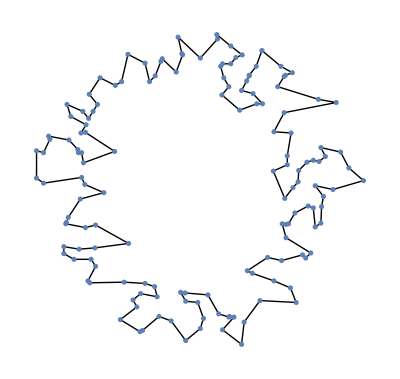

```mathematica
{distcir,tourcir} = FindShortestTour[set3]
pointPlot=ListPlot[set3->Range[numPoints1],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[set3[[tourcir]]]],pointPlot]
```

The number of accepting :3820

Distance of current Tour:40.1254

The number of accepting :3929

Distance of current Tour:45.1345

The number of accepting :3968

Distance of current Tour:42.0309

The number of accepting :4011

Distance of current Tour:43.0036

The number of accepting :4052

Distance of current Tour:44.45

The number of accepting :3835

Distance of current Tour:41.4457

The number of accepting :3880

Distance of current Tour:41.9902

The number of accepting :3951

Distance of current Tour:44.9083

The number of accepting :3889

Distance of current Tour:43.3325

The number of accepting :4131

Distance of current Tour:44.2532

The number of accepting :4004

Distance of current Tour:41.936

The number of accepting :3863

Distance of current Tour:42.7554

The number of accepting :3820

Distance of current Tour:42.6543

The number of accepting :4035

Distance of current Tour:44.2624

The number of accepting :4019

Distance of current Tour:41.9341

The number of accepting :3913

Distance of current Tour:43.7942

The number of accepting :4032

Distance of current Tour:44.1489

The number of accepting :3985

Distance of current Tour:41.8448

The number of accepting :4086

Distance of current Tour:43.2358

The number of accepting :3875

Distance of current Tour:43.3656

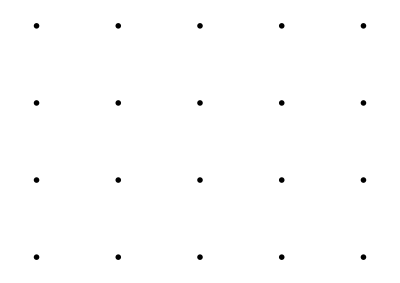

```mathematica
plot2s=Table[{distbest,tourbest} = findMinTour[set3 ,1,1.000069, 50000];
pointPlot=ListPlot[set3->Range[numPoints1],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[set3[[tourcir]]]],pointPlot],{i,20}];
GraphicsGrid[Partition[plot2s,5]]
```

#### What is the acceptance rate differs for our simulated annealing process?

To answer the above questions I made a loop so that I can extract the iteration number from our simulated annealing.

```mathematica
findMinTour1[points_,βstart_,βinc_,numIter_]:=Module[{n=Length[points],currTour,currDist,β=βstart,propTour,Δf,fVals=Table[0,numIter],ρ,j,k,jprev,knext,account,acceptIterations={},rejectIterations={}},currTour=Range[n];
currDist=distTour[points,currTour];
fVals[[1]]=currDist;
account=0;
Do[propTour=currTour;
{j,k}=RandomSample[Range[n],2];
If[j>k,{j,k}={k,j}];
While[j==1&&k==n,{j,k}=RandomSample[Range[n],2]];
If[j>k,{j,k}={k,j}];
propTour[[j;;k]]=Reverse[currTour[[j;;k]]];
jprev=If[j>1,j-1,n];
knext=If[k<n,k+1,1];
a=EuclideanDistance[points[[currTour[[k]]]],points[[currTour[[jprev]]]]];
b=EuclideanDistance[points[[currTour[[j]]]],points[[currTour[[knext]]]]];
c=EuclideanDistance[points[[currTour[[j]]]],points[[currTour[[jprev]]]]];
d=EuclideanDistance[points[[currTour[[k]]]],points[[currTour[[knext]]]]];
Δf=a+b-c-d;
β*=βinc;
ρ=Exp[-β*Δf];
If[RandomReal[]<ρ||Δf<0,
currTour=propTour;
currDist=currDist+Δf;
account+=1;
AppendTo[acceptIterations,i],
AppendTo[rejectIterations,i]];
fVals[[i]]=currDist;,{i,2,numIter}];
propTour=Append[propTour,propTour[[1]]];
(*Print["Shortest tour: ",propTour];(*Add the last position to the first position so we have fully connected path*)
Print["The number of accepting :",account];
Print["Distance of current Tour:",currDist];*)
(*Print["Accepting iterations: ",acceptIterations];
Print["Rejecting iterations: ",rejectIterations];*)
Print["Acceptance rate: ",(account/numIter)];(*This line is added to calculate the acceptance rate*)
{account,acceptIterations,rejectIterations}]
```

```mathematica
{account,acceptIterations,rejectIterations} = findMinTour1[points,1,1.0001, 200 ];
```

Acceptance rate: 177/200

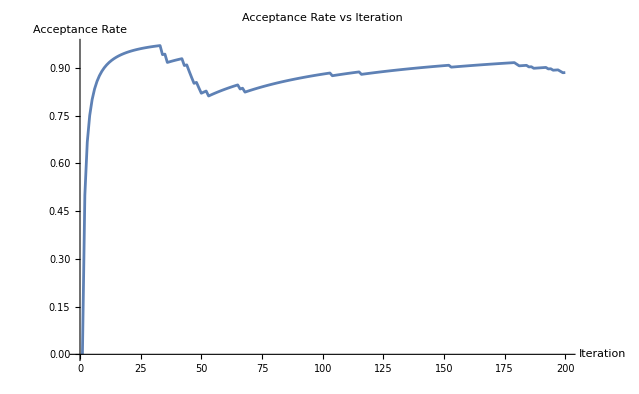

```mathematica
numIter =200;
acceptanceRate=Table[Count[acceptIterations,x_/;x<=i]/i,{i,1,numIter}];(*Code to match the succes with its repspective interation*)
ListLinePlot[acceptanceRate,PlotLabel->"Acceptance Rate vs Iteration",AxesLabel->{"Iteration","Acceptance Rate"}]
```

```mathematica
{account10,acceptIterations10,rejectIterations10} = findMinTour1[points10,1,1.0001,20000];
```

Acceptance rate: 2579/4000

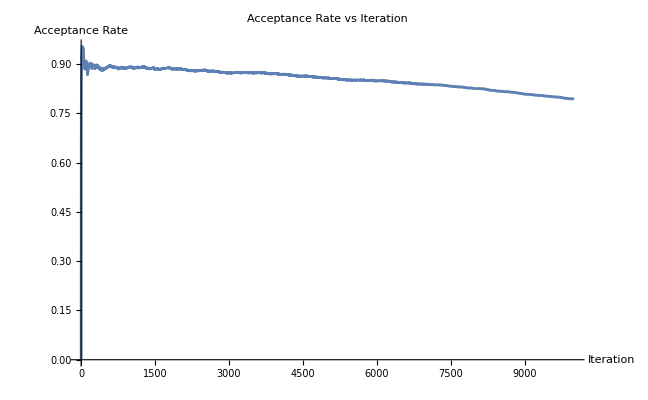

```mathematica
numIter =10000;
acceptanceRate10=Table[Count[acceptIterations10,x_/;x<=i]/i,{i,1,numIter}];
ListLinePlot[acceptanceRate10,PlotLabel->"Acceptance Rate vs Iteration",AxesLabel->{"Iteration","Acceptance Rate"}]
```

This confirm our discussion where we should have a bunch of rejecting at the beginning of the simulated annealing algorithm and then we get increasing more acceptance rate in the process. The reason why there might be a spike is that we can hit a local minimum. Hence it has to get out that somehow there for even though it’s not the optimal path.

#### From here we want to see how changes in the beta increment help us find the optimal TSP path

From my exploration above, I noticed that my simualtd anneling can be achived better with different increment of β.

```mathematica
listofbetaincrease=Range[1.00001,1.009,0.0001]
```

{1.00001,1.00011,1.00021,1.00031,1.00041,1.00051,1.00061,1.00071,1.00081,1.00091,1.00101,1.00111,1.00121,1.00131,1.00141,1.00151,1.00161,1.00171,1.00181,1.00191,1.00201,1.00211,1.00221,1.00231,1.00241,1.00251,1.00261,1.00271,1.00281,1.00291,1.00301,1.00311,1.00321,1.00331,1.00341,1.00351,1.00361,1.00371,1.00381,1.00391,1.00401,1.00411,1.00421,1.00431,1.00441,1.00451,1.00461,1.00471,1.00481,1.00491,1.00501,1.00511,1.00521,1.00531,1.00541,1.00551,1.00561,1.00571,1.00581,1.00591,1.00601,1.00611,1.00621,1.00631,1.00641,1.00651,1.00661,1.00671,1.00681,1.00691,1.00701,1.00711,1.00721,1.00731,1.00741,1.00751,1.00761,1.00771,1.00781,1.00791,1.00801,1.00811,1.00821,1.00831,1.00841,1.00851,1.00861,1.00871,1.00881,1.00891}

```mathematica
tablebetaincrease=Table[{beta,findMinTour[points10,1,beta,400]},{beta,listofbetaincrease}]
```

The number of accepting :341

Distance of current Tour:4.60286

The number of accepting :355

Distance of current Tour:4.44372

The number of accepting :352

Distance of current Tour:4.51374

The number of accepting :357

Distance of current Tour:5.21341

The number of accepting :346

Distance of current Tour:3.85024

The number of accepting :336

Distance of current Tour:3.61751

The number of accepting :346

Distance of current Tour:5.19073

The number of accepting :330

Distance of current Tour:5.13689

The number of accepting :348

Distance of current Tour:4.1588

The number of accepting :349

Distance of current Tour:4.72416

The number of accepting :339

Distance of current Tour:3.46156

The number of accepting :360

Distance of current Tour:4.63822

The number of accepting :333

Distance of current Tour:5.47621

The number of accepting :338

Distance of current Tour:4.37955

The number of accepting :312

Distance of current Tour:4.06651

The number of accepting :328

Distance of current Tour:4.08291

The number of accepting :340

Distance of current Tour:5.01859

The number of accepting :329

Distance of current Tour:4.38885

The number of accepting :325

Distance of current Tour:4.29715

The number of accepting :332

Distance of current Tour:4.13853

The number of accepting :325

Distance of current Tour:4.42577

The number of accepting :318

Distance of current Tour:4.06092

The number of accepting :334

Distance of current Tour:4.83365

The number of accepting :336

Distance of current Tour:3.96239

The number of accepting :315

Distance of current Tour:4.74542

The number of accepting :325

Distance of current Tour:4.80392

The number of accepting :315

Distance of current Tour:4.36266

The number of accepting :326

Distance of current Tour:4.27336

The number of accepting :312

Distance of current Tour:4.34134

The number of accepting :292

Distance of current Tour:4.58185

The number of accepting :309

Distance of current Tour:4.7388

The number of accepting :307

Distance of current Tour:4.12119

The number of accepting :307

Distance of current Tour:3.8557

The number of accepting :324

Distance of current Tour:4.34088

The number of accepting :293

Distance of current Tour:3.83587

The number of accepting :296

Distance of current Tour:3.99825

The number of accepting :304

Distance of current Tour:3.84324

The number of accepting :305

Distance of current Tour:4.01936

The number of accepting :295

Distance of current Tour:3.60291

The number of accepting :307

Distance of current Tour:4.14145

The number of accepting :281

Distance of current Tour:3.70246

The number of accepting :286

Distance of current Tour:4.06011

The number of accepting :284

Distance of current Tour:4.04857

The number of accepting :275

Distance of current Tour:3.81395

The number of accepting :282

Distance of current Tour:3.84435

The number of accepting :289

Distance of current Tour:2.87634

The number of accepting :250

Distance of current Tour:3.6677

The number of accepting :293

Distance of current Tour:3.64994

The number of accepting :252

Distance of current Tour:3.7396

The number of accepting :256

Distance of current Tour:3.83256

The number of accepting :248

Distance of current Tour:3.22628

The number of accepting :253

Distance of current Tour:3.7147

The number of accepting :257

Distance of current Tour:3.50947

The number of accepting :236

Distance of current Tour:3.72278

The number of accepting :249

Distance of current Tour:3.25368

The number of accepting :240

Distance of current Tour:3.27258

The number of accepting :268

Distance of current Tour:3.46487

The number of accepting :239

Distance of current Tour:2.89124

The number of accepting :242

Distance of current Tour:3.54372

The number of accepting :215

Distance of current Tour:3.58616

The number of accepting :228

Distance of current Tour:3.21468

The number of accepting :211

Distance of current Tour:0.412515

The number of accepting :239

Distance of current Tour:3.44237

The number of accepting :230

Distance of current Tour:3.01453

The number of accepting :224

Distance of current Tour:3.30345

The number of accepting :211

Distance of current Tour:3.32103

The number of accepting :211

Distance of current Tour:2.89124

The number of accepting :221

Distance of current Tour:2.93205

The number of accepting :195

Distance of current Tour:3.06337

The number of accepting :199

Distance of current Tour:2.93205

The number of accepting :211

Distance of current Tour:2.08313

The number of accepting :217

Distance of current Tour:3.28451

The number of accepting :225

Distance of current Tour:3.33817

The number of accepting :193

Distance of current Tour:2.89124

The number of accepting :199

Distance of current Tour:3.01453

The number of accepting :220

Distance of current Tour:3.14326

The number of accepting :198

Distance of current Tour:2.77872

The number of accepting :182

Distance of current Tour:3.22354

The number of accepting :203

Distance of current Tour:3.28451

The number of accepting :206

Distance of current Tour:3.27121

The number of accepting :204

Distance of current Tour:1.86989

The number of accepting :174

Distance of current Tour:2.89124

The number of accepting :187

Distance of current Tour:2.93205

The number of accepting :191

Distance of current Tour:2.89124

The number of accepting :220

Distance of current Tour:3.26779

The number of accepting :182

Distance of current Tour:2.89124

The number of accepting :170

Distance of current Tour:2.89124

The number of accepting :165

Distance of current Tour:2.89124

The number of accepting :158

Distance of current Tour:2.7138

The number of accepting :169

Distance of current Tour:3.05265

{{1.00001,{4.60286,{3,9,10,5,6,4,1,8,2,7,3}}},{1.00011,{4.44372,{9,6,1,7,10,5,8,2,3,4,9}}},{1.00021,{4.51374,{9,7,6,3,2,8,10,5,1,4,9}}},{1.00031,{5.21341,{8,10,1,2,3,5,7,9,4,6,8}}},{1.00041,{3.85024,{6,7,5,3,10,8,9,1,4,2,6}}},{1.00051,{3.61751,{7,2,6,10,5,3,9,8,4,1,7}}},{1.00061,{5.19073,{2,9,8,3,7,10,4,6,1,5,2}}},{1.00071,{5.13689,{5,7,4,6,8,2,1,9,10,3,5}}},{1.00081,{4.1588,{4,3,8,1,2,9,5,7,6,10,4}}},{1.00091,{4.72416,{9,7,5,10,3,6,2,4,8,1,9}}},{1.00101,{3.46156,{5,6,8,7,2,4,10,9,3,1,5}}},{1.00111,{4.63822,{7,4,8,5,10,3,9,2,6,1,7}}},{1.00121,{5.47621,{8,1,7,3,4,10,2,9,6,5,8}}},{1.00131,{4.37955,{9,5,7,6,4,3,1,8,10,2,9}}},{1.00141,{4.06651,{3,4,5,10,1,6,7,8,2,9,3}}},{1.00151,{4.08291,{4,1,8,7,2,10,5,6,9,3,4}}},{1.00161,{5.01859,{7,6,8,5,10,1,9,4,2,3,7}}},{1.00171,{4.38885,{8,1,5,2,6,4,3,7,10,9,8}}},{1.00181,{4.29715,{4,9,5,2,3,10,8,7,6,1,4}}},{1.00191,{4.13853,{2,6,7,9,5,4,10,3,1,8,2}}},{1.00201,{4.42577,{7,10,4,6,2,8,3,1,9,5,7}}},{1.00211,{4.06092,{4,2,1,5,6,7,10,9,3,8,4}}},{1.00221,{4.83365,{2,5,10,7,4,9,3,6,1,8,2}}},{1.00231,{3.96239,{7,2,8,5,9,6,3,4,1,10,7}}},{1.00241,{4.74542,{1,10,9,8,7,3,6,2,5,4,1}}},{1.00251,{4.80392,{5,1,2,4,10,3,7,6,8,9,5}}},{1.00261,{4.36266,{8,1,6,2,5,4,10,7,9,3,8}}},{1.00271,{4.27336,{2,1,7,9,5,6,3,4,10,8,2}}},{1.00281,{4.34134,{7,6,8,10,3,4,9,5,2,1,7}}},{1.00291,{4.58185,{8,5,6,2,1,10,4,3,9,7,8}}},{1.00301,{4.7388,{7,5,3,2,6,1,9,4,10,8,7}}},{1.00311,{4.12119,{7,6,2,9,3,5,10,8,4,1,7}}},{1.00321,{3.8557,{8,1,4,2,6,7,3,5,9,10,8}}},{1.00331,{4.34088,{2,7,9,10,8,6,1,5,4,3,2}}},{1.00341,{3.83587,{4,1,7,9,2,6,5,10,8,3,4}}},{1.00351,{3.99825,{5,2,6,7,1,4,9,3,8,10,5}}},{1.00361,{3.84324,{1,6,3,8,9,10,4,5,2,7,1}}},{1.00371,{4.01936,{10,9,8,4,5,6,2,1,3,7,10}}},{1.00381,{3.60291,{2,6,9,10,4,3,1,8,7,5,2}}},{1.00391,{4.14145,{7,2,4,8,5,1,3,6,10,9,7}}},{1.00401,{3.70246,{10,9,7,2,6,8,1,4,3,5,10}}},{1.00411,{4.06011,{5,8,9,4,3,2,6,7,1,10,5}}},{1.00421,{4.04857,{5,6,1,3,4,10,9,8,2,7,5}}},{1.00431,{3.81395,{5,2,1,6,8,3,4,9,7,10,5}}},{1.00441,{3.84435,{9,10,4,2,7,6,1,8,3,5,9}}},{1.00451,{2.87634,{7,8,2,6,4,3,1,9,10,5,7}}},{1.00461,{3.6677,{2,8,10,4,3,9,1,5,7,6,2}}},{1.00471,{3.64994,{7,8,5,9,4,3,10,2,1,6,7}}},{1.00481,{3.7396,{10,9,2,3,7,6,1,4,5,8,10}}},{1.00491,{3.83256,{8,6,1,3,4,2,7,9,10,5,8}}},{1.00501,{3.22628,{4,3,8,10,2,7,1,6,5,9,4}}},{1.00511,{3.7147,{9,2,1,6,7,4,3,5,8,10,9}}},{1.00521,{3.50947,{5,3,9,10,2,7,6,1,4,8,5}}},{1.00531,{3.72278,{4,5,10,9,3,7,6,2,1,8,4}}},{1.00541,{3.25368,{2,1,6,7,10,9,5,4,3,8,2}}},{1.00551,{3.27258,{5,10,7,6,2,1,8,9,4,3,5}}},{1.00561,{3.46487,{6,2,1,3,7,8,9,5,10,4,6}}},{1.00571,{2.89124,{1,2,6,7,10,9,3,8,5,4,1}}},{1.00581,{3.54372,{4,10,8,2,7,6,1,5,9,3,4}}},{1.00591,{3.58616,{5,4,3,6,2,1,10,9,8,7,5}}},{1.00601,{3.21468,{6,5,7,10,9,4,3,8,1,2,6}}},{1.00611,{0.412515,{5,7,4,3,1,2,6,8,10,9,5}}},{1.00621,{3.44237,{5,8,1,2,6,3,7,4,9,10,5}}},{1.00631,{3.01453,{8,3,4,5,10,9,7,6,2,1,8}}},{1.00641,{3.30345,{8,7,6,2,4,3,1,10,9,5,8}}},{1.00651,{3.32103,{1,2,8,4,6,7,10,9,5,3,1}}},{1.00661,{2.89124,{9,5,8,3,6,2,1,4,7,10,9}}},{1.00671,{2.93205,{5,8,4,3,2,1,6,7,10,9,5}}},{1.00681,{3.06337,{1,9,10,8,3,4,5,7,6,2,1}}},{1.00691,{2.93205,{3,6,2,1,7,10,9,5,8,4,3}}},{1.00701,{2.08313,{10,7,2,8,3,4,1,6,5,9,10}}},{1.00711,{3.28451,{10,4,3,9,1,2,6,7,5,8,10}}},{1.00721,{3.33817,{2,6,7,3,1,4,8,9,10,5,2}}},{1.00731,{2.89124,{5,8,3,4,1,2,10,7,6,9,5}}},{1.00741,{3.01453,{4,3,8,5,10,6,7,9,2,1,4}}},{1.00751,{3.14326,{6,7,10,9,8,3,5,4,1,2,6}}},{1.00761,{2.77872,{6,2,7,5,10,9,8,4,3,1,6}}},{1.00771,{3.22354,{5,3,1,4,2,6,7,10,9,8,5}}},{1.00781,{3.28451,{1,2,6,7,5,8,10,9,3,4,1}}},{1.00791,{3.27121,{1,8,2,6,7,5,9,10,3,4,1}}},{1.00801,{1.86989,{2,1,5,10,9,8,3,4,7,6,2}}},{1.00811,{2.89124,{9,5,8,3,2,1,4,6,7,10,9}}},{1.00821,{2.93205,{5,7,10,9,6,2,1,3,4,8,5}}},{1.00831,{2.89124,{5,9,10,7,6,2,1,8,3,4,5}}},{1.00841,{3.26779,{9,5,10,7,3,8,4,1,2,6,9}}},{1.00851,{2.89124,{2,6,7,10,9,5,8,1,4,3,2}}},{1.00861,{2.89124,{4,8,5,9,10,7,6,2,1,3,4}}},{1.00871,{2.89124,{3,8,5,9,10,7,1,2,6,4,3}}},{1.00881,{2.7138,{6,4,3,1,2,8,5,10,9,7,6}}},{1.00891,{3.05265,{8,3,6,2,1,4,7,10,5,9,8}}}}

```mathematica
bestbeta=MinimalBy[tablebetaincrease,#[[2,1]]&]
```

{{1.00611,{0.412515,{5,7,4,3,1,2,6,8,10,9,5}}}}

Caveat: We can not increase increment to much it have to be small at first or else we are going to hit the local maximum to fast we skip to many trials/paths . Note that, the number of points is a big factor to this hypothesis and observation.

```mathematica
{distSA10,tourSA10}=findMinTour[points10,1,1.00611,800];
pointPlot=ListPlot[points10->Range[numPoints10],PlotRange->{{0,1},{0,1}},AspectRatio->1];
Show[Graphics[Line[points10[[tourSA10]]]],pointPlot]
```

The number of accepting :267

Distance of current Tour:2.89124

-Graphics-